## Recoil pressure

This equation calculates the recoil pressure according to the eq.11
in the paper J. Phys. D: Appl. Phys. 30 2541:

```mathematica
pr[T_]:= A B0 Sqrt[T]*Exp[-U/T];
```

```mathematica
Na = 6.02214076 10^23; kb= 1.380649 10^-23;Lv=6088;A=0.55; B0=3.9 10^-13; Ma=55.845; U = Ma Lv / (Na kb);
```

```mathematica
U
```

40890.7

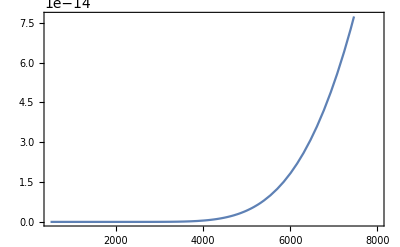

```mathematica
Plot[pr[T],{T,500,8000},Frame->True]
```

Evaporation velocity:

```mathematica
V0 = 5100;
vel[T_]:= V0 Exp[-U/T];
```

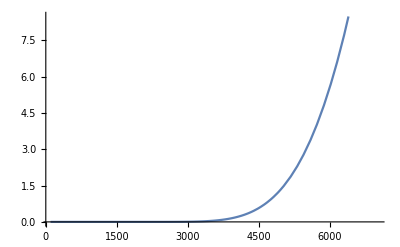

```mathematica
Plot[vel[T],{T,100,7000}]
```

Recoil pressure calculate using equation from “Laser processing and chemistry”:

```mathematica
Χ=49901.35778113031; Tb=3560.0; P0=101325;
p[T_]:= P0 Exp[Χ (1/Tb-1/T)];
```

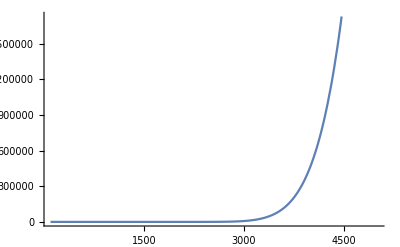

```mathematica
Plot[p[T],{T,100,5000}]
```

```mathematica
p[4000]
```

101338.

```mathematica
Exp[49901.35778113031*(1/3560-1/4000)]
```

4.67344

```mathematica
4.3 / (8.617×10^-5)
```

49901.4